# Simple Task 6

Brian Carlson 2-14-2014

## Problem 1.

1.  Write a function with is given a list of pairs {name, cost}  indicating some purchases and the name of a purchaser. The function determines and returns the total cost of all the purchases associated with that name.

```mathematica
purchases[list_,name_]:=Total[Cases[list,{name,n_}->n]]
```

#### Test Cases

```mathematica
purchases[{{"Cam",12.30},{"Tyler",2.00},{"Sam",123.85},{"Sam",4000.99},{"Tyler",3.00},{"Sam",20.00}},"Sam"]
```

4144.84

```mathematica
123.85+4000.99+20
```

4144.84

```mathematica
purchases[{{"Cam",12.30},{"Tyler",2.00},{"Sam",123.85},{"Sam",4000.99},{"Tyler",3.00},{"Sam",20.00}},"Tyler"]
```

5.

```mathematica
2+3
```

5

## Problem 2.

2. Create a function drunkwalk[ystart,length] that has the drunk starting at y-value ystart and x-value 0 and making length moves.

```mathematica
drunkwalk[ystart_,length_]:= Module[{points={},x,y=ystart},
For[x=0,x<length,x++,
AppendTo[points,{x,y}];
If[RandomInteger[]==1,y++,y--]
];
ListPlot[{points,If[MatrixQ[Cases[points,{a_,0}]],Cases[points,{a_,0}],{points[[1]]}]},
Joined->{True,False},PlotStyle->{Black,Directive[PointSize[Large],Yellow]},
(*We set the styles for each list of points*)
PlotLegends->SwatchLegend[{Black,Yellow},{"Line",If[MatrixQ[Cases[points,{a_,0}]],"Y-values equal to 0","Start Walk"]},LegendMarkers->Graphics[{EdgeForm[Black],Rectangle[]}],LegendLabel->"Legend",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],
PlotRange->{Min[#[[2]]&/@points]-5,Max[#[[2]]&/@points +5]},
AxesLabel->{"Time","Variation From Path"}]
]
```

#### Test Cases

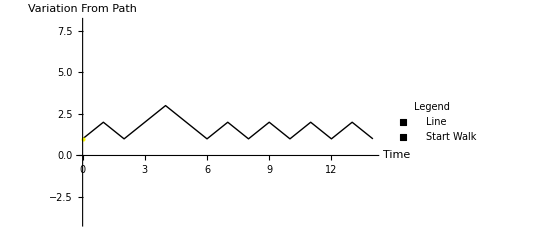

```mathematica
drunkwalk[1,15]
```

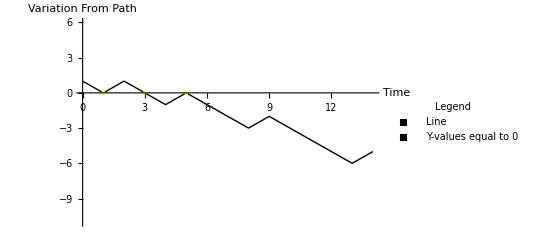

```mathematica
drunkwalk[1,15]
```

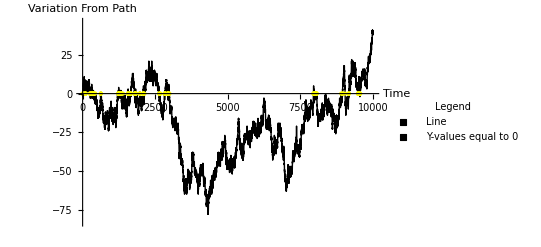

```mathematica
drunkwalk[0,10000]
```